# Data generation

## Data format

Artificial data generation for clulstering varidity.

Data structire:
<Model and annotation>
;
<Dimension>[\tab]<Number of clusters>[\tab]<Number of samples>[\tab]<Number of background points>
;
<Cluster centers (model): matrix with tab delimiter>
;
<Samples: matrix with tab delimiter>
;

## Preparation

```mathematica
dir="/Users/amanokou/gitsrc/"
```

/Users/amanokou/gitsrc/

```mathematica
Get[dir<>"MATH_SCRIPT/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory[dir<>"ClusteringAdequation"]
```

/Users/amanokou/gitsrc/ClusteringAdequation

## Programs

```mathematica
strDataToExportStr[n_]:=StringJoin[Riffle[{anntS[n],dimS[n],centersS[n],samplesS[n]},";\n"]]
```

```mathematica
distanceMat[mat_]:=Module[
{n},
n=Length[mat];
Table[EuclideanDistance[mat[[i]],mat[[j]]],{i,n},{j,n}]
]
```

## 2D

### data 1 (general)

```mathematica
anntS[1]="Model: central random, circles, one radius, triangle.\n"
```

Model: central random, circles, one radius, triangle.

```mathematica
dim[1]=2;
numClass[1]=3;
numSample[1]={100,100,100};
numBG[1]={0};
```

```mathematica
dimS[1]=StringJoin[Riffle[{ToString[dim[1]],ToString[numClass[1]],ToString[numSample[1]],ToString[numBG[1]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
centers[1]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[1] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[1]=ExportString[centers[1],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844388
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[1]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[1]=Tr[Flatten[distanceMat[centers[1]]]]/(numClass[1]^2-numClass[1])
```

1.73205

```mathematica
samples[1]=Table[Map[#+centers[1][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[1]/2}],RandomReal[{0,2Pi}]}],{numSample[1][[n]]}]],{n,numClass[1]}];
```

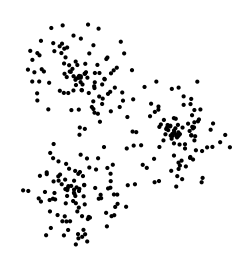

```mathematica
Graphics[Map[Point[#]&,samples[1],{2}]]
```

```mathematica
samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";
```

```mathematica
(*Export["data1.tsv",strDataToExportStr[1],"String"]*)
```

### data 2 (unbalanced)

```mathematica
anntS[2]="Model: unbalanced central random, circles, radiuses.\n"
```

Model: unbalanced central random, circles, radiuses.

```mathematica
dim[2]=2;
numClass[2]=3;
numSample[2]={200,100,50};
numBG[2]={0};
```

```mathematica
dimS[2]=StringJoin[Riffle[{ToString[dim[2]],ToString[numClass[2]],ToString[numSample[2]],ToString[numBG[2]]},"\t"],"\n"]
```

2	3	{200, 100, 50}	{0}

```mathematica
centers[2]={{0,0},{0.5,-1},{-0.5,-0.75}}
```

{{0,0},{0.5,-1},{-0.5,-0.75}}

```mathematica
centersS[2]=ExportString[centers[2],"TSV"]<>"\n"
```

0	0
0.5	-1
-0.5	-0.75

```mathematica
distanceMat[centers[2]]
```

{{0,1.11803,0.901388},{1.11803,0.,1.03078},{0.901388,1.03078,0.}}

```mathematica
distMean[2]=Tr[Flatten[distanceMat[centers[2]]]]/(numClass[2]^2-numClass[2])
```

1.01673

```mathematica
radius[2]={distMean[2]*0.6,distMean[2]*0.4,distMean[2]*0.2}
```

{0.61004,0.406693,0.203347}

```mathematica
samples[2]=Table[Map[#+centers[2][[n]]&,Table[polarToxy[{RandomReal[{0,radius[2][[n]]}],RandomReal[{0,2Pi}]}],{numSample[2][[n]]}]],{n,numClass[2]}];
```

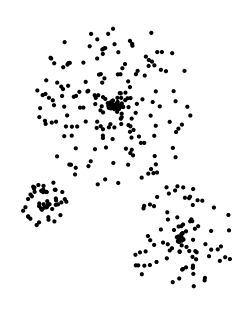

```mathematica
Graphics[Map[Point[#]&,samples[2],{2}]]
```

```mathematica
samplesS[2]=ExportString[Flatten[samples[2],1],"TSV"]<>"\n";
```

```mathematica
(*Export["data2.tsv",strDataToExportStr[2],"String"]*)
```

### data 3 (noisy)

```mathematica
anntS[3]="Model: central random + noise, circles, one radius, triangle.\n"
```

Model: central random + noise, circles, one radius, triangle.

```mathematica
dim[3]=2;
numClass[3]=3;
numSample[3]={100,100,100};
numBG[3]={150};
```

```mathematica
dimS[3]=StringJoin[Riffle[{ToString[dim[3]],ToString[numClass[3]],ToString[numSample[3]],ToString[numBG[3]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{150}

```mathematica
centers[3]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[3] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[3]=ExportString[centers[3],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844388
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[3]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[3]=Tr[Flatten[distanceMat[centers[3]]]]/(numClass[3]^2-numClass[3])
```

1.73205

```mathematica
samples[3,"class"]=Table[Map[#+centers[3][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[3]/3}],RandomReal[{0,2Pi}]}],{numSample[3][[n]]}]],{n,numClass[3]}];
```

```mathematica
maxmin[3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[3,"class"],1]]]
```

{{1.52987,-1.01582},{1.43231,-1.4003}}

```mathematica
samples[3,"background"]=Table[{RandomReal[maxmin[3][[1]]],RandomReal[maxmin[3][[2]]]},{numBG[3][[1]]}];
```

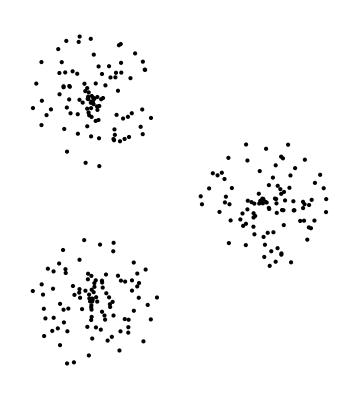

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[3,"class"],1]]]
```

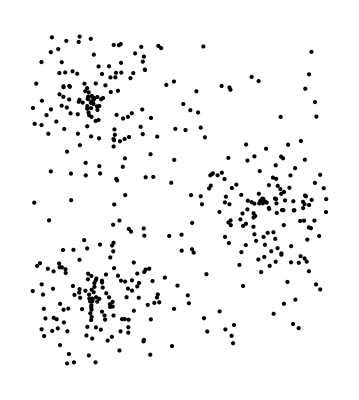

```mathematica
Graphics[Map[Point[#]&,Join[Flatten[samples[3,"class"],1],samples[3,"background"]]]]
```

```mathematica
samplesS[3]=ExportString[Join[Flatten[samples[3,"class"],1],samples[3,"background"]],"TSV"]<>"\n";
```

```mathematica
(*Export["data3.tsv",strDataToExportStr[3],"String"]*)
```

data3.tsv

### data 4 (sub class)

```mathematica
anntS[4]="Model: central random , circles, one radius, subclusters.\n"
```

Model: central random , circles, one radius, subclusters.

```mathematica
dim[4]=2;
numClass[4]=4;
numSample[4]={100,100,100,100};
numBG[4]={0};
```

```mathematica
dimS[4]=StringJoin[Riffle[{ToString[dim[4]],ToString[numClass[4]],ToString[numSample[4]],ToString[numBG[4]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[4]={{2,1},{2,-1},{-2,1},{-2,-1}}
```

{{2,1},{2,-1},{-2,1},{-2,-1}}

```mathematica
centersS[4]=ExportString[centers[4],"TSV"]<>"\n"
```

2	1
2	-1
-2	1
-2	-1

```mathematica
distMean[4]=Tr[Flatten[distanceMat[centers[4]]//N]]/(numClass[4]^2-numClass[4])
```

3.49071

```mathematica
samples[4,"class"]=Table[Map[#+centers[4][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[4]/4}],RandomReal[{0,2Pi}]}],{numSample[4][[n]]}]],{n,numClass[4]}];
```

```mathematica
maxmin[4]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[4,"class"],1]]]
```

{{2.84335,-2.83036},{1.80755,-1.85934}}

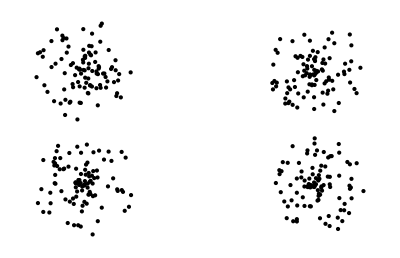

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[4,"class"],1]]]
```

```mathematica
(*samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";*)
```

```mathematica
samplesS[4]=ExportString[Flatten[samples[4,"class"],1],"TSV"]<>"\n";
```

```mathematica
(*samplesS[4]=ExportString[Join[Flatten[samples[4,"class"],1],samples[4,"background"]],"TSV"]<>"\n";*)
```

```mathematica
(*Export["data4.tsv",strDataToExportStr[4],"String"]*)
```

### data 5 (ring + disc)

```mathematica
anntS[5]="Model: central random , disc + ring.\n"
```

Model: central random , disc + ring.

```mathematica
dim[5]=2;
numClass[5]=2;
numSample[5]={100,200};
numBG[5]={0};
```

```mathematica
dimS[5]=StringJoin[Riffle[{ToString[dim[5]],ToString[numClass[5]],ToString[numSample[5]],ToString[numBG[5]]},"\t"],"\n"]
```

2	2	{100, 200}	{0}

```mathematica
centers[5]={{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
centersS[5]=ExportString[centers[5],"TSV"]<>"\n"
```

0	0
0	0

```mathematica
(*distMean[4]=Tr[Flatten[distanceMat[centers[4]]//N]]/(numClass[4]^2-numClass[4])*)
```

```mathematica
(*samples[4,"class"]=Table[Map[#+centers[4][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[4]/4}],RandomReal[{0,2Pi}]}],{numSample[4][[n]]}]],{n,numClass[4]}];*)
```

```mathematica
samples[5,"disc"]=Map[polarToxy[#]&,Table[{RandomReal[{0,1}],RandomReal[{0,2 Pi}]},{numSample[5][[1]]}]];
```

```mathematica
samples[5,"ring"]=Map[polarToxy[#]&,Table[{RandomReal[{1.5,2}],RandomReal[{0,2 Pi}]},{numSample[5][[2]]}]];
```

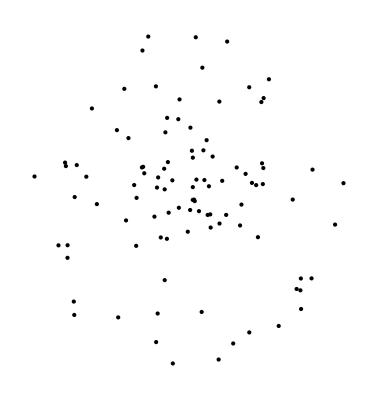

```mathematica
Graphics[Map[Point[#]&,samples[5,"disc"]]]
```

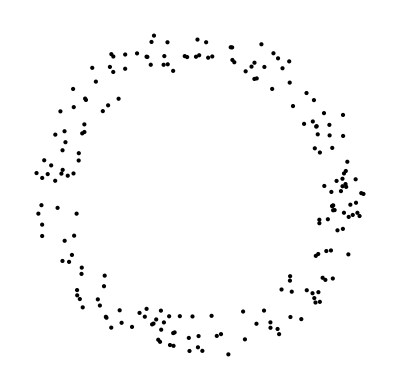

```mathematica
Graphics[Map[Point[#]&,samples[5,"ring"]]]
```

```mathematica
samples[5,"class"]=Join[samples[5,"disc"],samples[5,"ring"]];
```

```mathematica
(*samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";*)
```

```mathematica
(*samplesS[5]=ExportString[Flatten[samples[5,"class"],1],"TSV"]<>"\n";*)
```

```mathematica
samplesS[5]=ExportString[samples[5,"class"],"TSV"]<>"\n";
```

```mathematica
(*samplesS[4]=ExportString[Join[Flatten[samples[4,"class"],1],samples[4,"background"]],"TSV"]<>"\n";*)
```

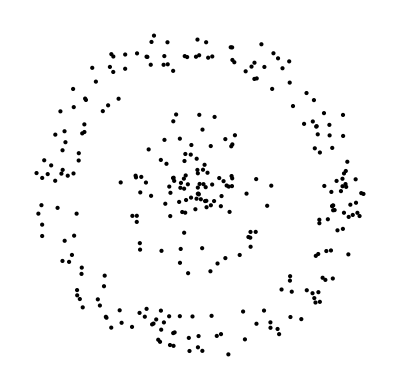

```mathematica
Map[Point[#]&,samples[5,"class"]]//Graphics
```

```mathematica
SetDirectory["/Users/kouamano/gitsrc/ClusteringAdequation/generative-data"]
```

/Users/kouamano/gitsrc/ClusteringAdequation/generative-data

```mathematica
Export["data5.tsv",strDataToExportStr[5],"String"]
```

data5.tsv

### data 6 (spiral)

```mathematica
anntS[6]="Model: spiral x 3.\n"
```

Model: spiral x 3.

```mathematica
dim[6]=2;
numClass[6]=3;
numSample[6]={100,100,100};
numBG[6]={0};
```

```mathematica
dimS[6]=StringJoin[Riffle[{ToString[dim[6]],ToString[numClass[6]],ToString[numSample[6]],ToString[numBG[6]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
origins[6]={{0,0},{0,0},{0,0}}
```

{{0,0},{0,0},{0,0}}

```mathematica
(samples[6,0]=Map[polarToxy[#]&,Table[{r,3r},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,0]=Mean[samples[6,0]]
```

{0.0684864,0.339278}

```mathematica
(samples[6,1]=Map[polarToxy[#]&,Table[{r,3r+(2Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,1]=Mean[samples[6,1]]
```

{-0.328066,-0.110328}

```mathematica
(samples[6,2]=Map[polarToxy[#]&,Table[{r,3r+(4Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,2]=Mean[samples[6,2]]
```

{0.25958,-0.22895}

```mathematica
centers[6]={center[6,0],center[6,1],center[6,2]}
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
centersS[6]=ExportString[centers[6],"TSV"]<>"\n"
```

0.06848640517315346	0.3392778825308757
-0.3280664678005077	-0.11032797457161272
0.25958006262735384	-0.22894990795926298

```mathematica
samples[6,"class"]=Join[samples[6,0],samples[6,1],samples[6,2]];
```

```mathematica
(*samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";*)
```

```mathematica
samplesS[6]=ExportString[samples[6,"class"],"TSV"]<>"\n";
```

```mathematica
(*samplesS[4]=ExportString[Join[Flatten[samples[4,"class"],1],samples[4,"background"]],"TSV"]<>"\n";*)
```

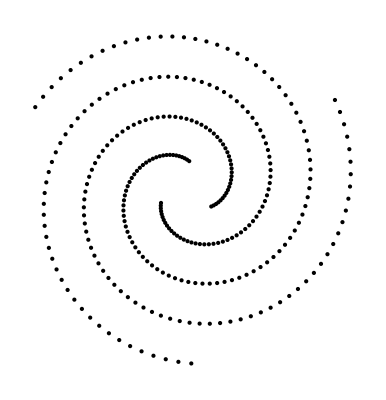

```mathematica
Map[Point[#]&,samples[6,"class"]]//Graphics
```

```mathematica
SetDirectory["/Users/kouamano/gitsrc/ClusteringAdequation/generative-data"]
```

/Users/kouamano/gitsrc/ClusteringAdequation/generative-data

```mathematica
(*Export["data6.tsv",strDataToExportStr[6],"String"]*)
```

data6.tsv

## 3D

### data 7 (chain)

```mathematica
anntS[7]="Model: double chain.\n"
```

Model: double chain.

```mathematica
dim[7]=3;
numClass[7]=2;
numSample[7]={150,150};
numBG[7]={0};
```

```mathematica
dimS[7]=StringJoin[Riffle[{ToString[dim[7]],ToString[numClass[7]],ToString[numSample[7]],ToString[numBG[7]]},"\t"],"\n"]
```

3	2	{150, 150}	{0}

```mathematica
centers[7]={{0,0,0},{1,0,0}}
```

{{0,0,0},{1,0,0}}

```mathematica
(*origins[6]={{0,0},{0,0},{0,0}}*)
```

```mathematica
centersS[7]=ExportString[centers[7],"TSV"]<>"\n"
```

0	0	0
1	0	0

//Under construcrion

```mathematica
samples[7,1]=Map[sPolarToxyz[#]&,Table[{1,Pi/2,ph},{ph,0,2Pi,2Pi/149}]];
```

```mathematica
Map[Point[#]&,samples[7,1]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,1]]//Graphics3D
```

-Graphics3D-

```mathematica
samples[7,2]=Map[sPolarToxyz[#]&,Table[{1,th,0},{th,0,2Pi,2Pi/149}]];
```

```mathematica
Map[Point[#]&,samples[7,2]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,2]]//Graphics3D
```

-Graphics3D-

```mathematica
(samples[7,"All"]=Join[samples[7,1],Map[#+centers[7][[2]]&,samples[7,2]]]//N)//Length
```

300

```mathematica
Map[Point[#]&,samples[7,"All"]]//Graphics3D
```

-Graphics3D-

```mathematica
samplesS[7]=ExportString[samples[7,"All"],"TSV"]<>"\n"
```

1.	0.	0.
0.9991110182465031	0.04215653233409721	0.
0.9964456535631284	0.08423811189212299	0.
0.9920086448710159	0.12616991916130652	0.
0.9858078810097003	0.16787740091854086	0.
0.9778543867110426	0.20928640278329308	0.
0.9681623029976587	0.25032330106138656	0.
0.956748862040698	0.29091513364524274	0.
0.9436343565216709	0.3309897297378454	0.
0.9288421035528028	0.3704758381697844	0.
0.9123984032200585	0.4093032540812346	0.
0.8943324918225493	0.44740294374363454	0.
0.8746764898914609	0.48470716729913665	0.
0.8534653450809199	0.5211495991996025	0.
0.8307367700323411	0.5566654461310071	0.
0.806531175322727	0.5911915622135863	0.
0.7808915976161361	0.6246665612729071	0.
0.7538636231460657	0.6570309259822452	0.
0.7254953066647915	0.6882271136822207	0.
0.6958370860037718	0.7181996586895454	0.
0.6649416923970246	0.7468952709129846	0.
0.6328640567269168	0.7742629306011943	0.
0.5996612118590604	0.800253979053977	0.
0.5653921912399589	0.8248222051356752	0.
0.5301179239376935	0.8479239274368838	0.
0.49390112631226357	0.8695180719384028	0.
0.4568061905081872	0.8895662450393438	0.
0.41889906996761844	0.9080328018195511	0.
0.3802471621675336	0.92488490941497	0.
0.34091918878947697	0.9400926053932799	0.
0.30098507353491866	0.9536288510260056	0.
0.2605158178034654	0.9654695793623906	0.
0.21958337445496293	0.9755937380195567	0.
0.178260519879937	0.9839833266128724	0.
0.13662072460582675	0.9906234287599799	0.
0.09473802266906833	0.9955022386015789	0.
0.052686879985279524	0.9986110817918139	0.
0.010542061951579538	0.9999444309209432	0.
-0.03162149948355883	0.9994999153428735	0.
-0.07372883904657901	0.9972783253900807	0.
-0.11570509142436135	0.9932836109684284	0.
-0.15747562437201776	0.9875228745343791	0.
-0.1989661714062997	0.9800063584670862	0.
-0.24010296384869492	0.9707474268578168	0.
-0.2808128619834461	0.959762541749086	0.
-0.3210234850972963	0.9470712338657457	0.
-0.36066334016975543	0.9326960678900685	0.
-0.3996619489850823	0.9166626023425661	0.
-0.4379499734399796	0.8989993441398727	0.
-0.4754593388242117	0.8797376979104871	0.
-0.512123354854955	0.8589119101584899	0.
-0.5478768342496869	0.8365590083745086	0.
-0.5826562086267955	0.8127187352021904	0.
-0.6163996415278423	0.7874334777772327	0.
-0.6490471383605285	0.7607481923646016	0.
-0.6805406530668909	0.7327103244279348	0.
-0.7108241913270748	0.7033697242732375	0.
-0.7398439101151906	0.6727785584168582	0.
-0.7675482134302499	0.6409912168353257	0.
-0.793887844031972	0.6080642162619564	0.
-0.8188159710183592	0.5740560997021646	0.
-0.8422882730893321	0.5390273323461351	0.
-0.8642630173483832	0.503040194063922	0.
-0.8847011335021446	0.466158668674112	0.
-0.9035662833259431	0.42844833018293066	0.
-0.9208249252718379	0.3899762261960517	0.
-0.9364463741042692	0.3508107587104009	0.
-0.9504028554572863	0.31102156249790225	0.
-0.9626695552163577	0.2706793812973941	0.
-0.9732246636369604	0.22985594203484355	0.
-0.9820494141215101	0.18862382729548932	0.
-0.9891281165856873	0.1470563462746542	0.
-0.9944481853548335	0.1052274044366709	0.
-0.9980001615408226	0.06321137211366354	0.
-0.9997777298596181	0.021082952277811057	0.
-0.9997777298596181	-0.021082952277811057	0.
-0.9980001615408226	-0.06321137211366354	0.
-0.9944481853548335	-0.1052274044366709	0.
-0.9891281165856873	-0.1470563462746542	0.
-0.9820494141215101	-0.18862382729548932	0.
-0.9732246636369604	-0.22985594203484355	0.
-0.9626695552163577	-0.2706793812973941	0.
-0.9504028554572863	-0.31102156249790225	0.
-0.9364463741042692	-0.3508107587104009	0.
-0.9208249252718379	-0.3899762261960517	0.
-0.9035662833259431	-0.42844833018293066	0.
-0.8847011335021446	-0.466158668674112	0.
-0.8642630173483832	-0.503040194063922	0.
-0.8422882730893321	-0.5390273323461351	0.
-0.8188159710183592	-0.5740560997021646	0.
-0.793887844031972	-0.6080642162619564	0.
-0.7675482134302499	-0.6409912168353257	0.
-0.7398439101151906	-0.6727785584168582	0.
-0.7108241913270748	-0.7033697242732375	0.
-0.6805406530668909	-0.7327103244279348	0.
-0.6490471383605285	-0.7607481923646016	0.
-0.6163996415278423	-0.7874334777772327	0.
-0.5826562086267955	-0.8127187352021904	0.
-0.5478768342496869	-0.8365590083745086	0.
-0.512123354854955	-0.8589119101584899	0.
-0.4754593388242117	-0.8797376979104871	0.
-0.4379499734399796	-0.8989993441398727	0.
-0.3996619489850823	-0.9166626023425661	0.
-0.36066334016975543	-0.9326960678900685	0.
-0.3210234850972963	-0.9470712338657457	0.
-0.2808128619834461	-0.959762541749086	0.
-0.24010296384869492	-0.9707474268578168	0.
-0.1989661714062997	-0.9800063584670862	0.
-0.15747562437201776	-0.9875228745343791	0.
-0.11570509142436135	-0.9932836109684284	0.
-0.07372883904657901	-0.9972783253900807	0.
-0.03162149948355883	-0.9994999153428735	0.
0.010542061951579538	-0.9999444309209432	0.
0.052686879985279524	-0.9986110817918139	0.
0.09473802266906833	-0.9955022386015789	0.
0.13662072460582675	-0.9906234287599799	0.
0.178260519879937	-0.9839833266128724	0.
0.21958337445496293	-0.9755937380195567	0.
0.2605158178034654	-0.9654695793623906	0.
0.30098507353491866	-0.9536288510260056	0.
0.34091918878947697	-0.9400926053932799	0.
0.3802471621675336	-0.92488490941497	0.
0.41889906996761844	-0.9080328018195511	0.
0.4568061905081872	-0.8895662450393438	0.
0.49390112631226357	-0.8695180719384028	0.
0.5301179239376935	-0.8479239274368838	0.
0.5653921912399589	-0.8248222051356752	0.
0.5996612118590604	-0.800253979053977	0.
0.6328640567269168	-0.7742629306011943	0.
0.6649416923970246	-0.7468952709129846	0.
0.6958370860037718	-0.7181996586895454	0.
0.7254953066647915	-0.6882271136822207	0.
0.7538636231460657	-0.6570309259822452	0.
0.7808915976161361	-0.6246665612729071	0.
0.806531175322727	-0.5911915622135863	0.
0.8307367700323411	-0.5566654461310071	0.
0.8534653450809199	-0.5211495991996025	0.
0.8746764898914609	-0.48470716729913665	0.
0.8943324918225493	-0.44740294374363454	0.
0.9123984032200585	-0.4093032540812346	0.
0.9288421035528028	-0.3704758381697844	0.
0.9436343565216709	-0.3309897297378454	0.
0.956748862040698	-0.29091513364524274	0.
0.9681623029976587	-0.25032330106138656	0.
0.9778543867110426	-0.20928640278329308	0.
0.9858078810097003	-0.16787740091854086	0.
0.9920086448710159	-0.12616991916130652	0.
0.9964456535631284	-0.08423811189212299	0.
0.9991110182465031	-0.04215653233409721	0.
1.	0.	0.
1.	0.	1.
1.042156532334097	0.	0.9991110182465031
1.084238111892123	0.	0.9964456535631284
1.1261699191613066	0.	0.9920086448710159
1.1678774009185409	0.	0.9858078810097003
1.209286402783293	0.	0.9778543867110426
1.2503233010613866	0.	0.9681623029976587
1.2909151336452427	0.	0.956748862040698
1.3309897297378455	0.	0.9436343565216709
1.3704758381697844	0.	0.9288421035528028
1.4093032540812347	0.	0.9123984032200585
1.4474029437436347	0.	0.8943324918225493
1.4847071672991365	0.	0.8746764898914609
1.5211495991996025	0.	0.8534653450809199
1.556665446131007	0.	0.8307367700323411
1.5911915622135862	0.	0.806531175322727
1.6246665612729072	0.	0.7808915976161361
1.6570309259822453	0.	0.7538636231460657
1.6882271136822207	0.	0.7254953066647915
1.7181996586895454	0.	0.6958370860037718
1.7468952709129846	0.	0.6649416923970246
1.7742629306011943	0.	0.6328640567269168
1.800253979053977	0.	0.5996612118590604
1.8248222051356753	0.	0.5653921912399589
1.847923927436884	0.	0.5301179239376935
1.8695180719384028	0.	0.49390112631226357
1.8895662450393438	0.	0.4568061905081872
1.9080328018195511	0.	0.41889906996761844
1.92488490941497	0.	0.3802471621675336
1.9400926053932799	0.	0.34091918878947697
1.9536288510260056	0.	0.30098507353491866
1.9654695793623906	0.	0.2605158178034654
1.9755937380195567	0.	0.21958337445496293
1.9839833266128724	0.	0.178260519879937
1.9906234287599798	0.	0.13662072460582675
1.995502238601579	0.	0.09473802266906833
1.998611081791814	0.	0.052686879985279524
1.999944430920943	0.	0.010542061951579538
1.9994999153428736	0.	-0.03162149948355883
1.9972783253900808	0.	-0.07372883904657901
1.9932836109684284	0.	-0.11570509142436135
1.9875228745343791	0.	-0.15747562437201776
1.9800063584670862	0.	-0.1989661714062997
1.970747426857817	0.	-0.24010296384869492
1.959762541749086	0.	-0.2808128619834461
1.9470712338657457	0.	-0.3210234850972963
1.9326960678900686	0.	-0.36066334016975543
1.9166626023425661	0.	-0.3996619489850823
1.8989993441398727	0.	-0.4379499734399796
1.8797376979104872	0.	-0.4754593388242117
1.8589119101584899	0.	-0.512123354854955
1.8365590083745085	0.	-0.5478768342496869
1.8127187352021905	0.	-0.5826562086267955
1.7874334777772327	0.	-0.6163996415278423
1.7607481923646016	0.	-0.6490471383605285
1.7327103244279347	0.	-0.6805406530668909
1.7033697242732375	0.	-0.7108241913270748
1.6727785584168582	0.	-0.7398439101151906
1.6409912168353258	0.	-0.7675482134302499
1.6080642162619565	0.	-0.793887844031972
1.5740560997021646	0.	-0.8188159710183592
1.539027332346135	0.	-0.8422882730893321
1.503040194063922	0.	-0.8642630173483832
1.466158668674112	0.	-0.8847011335021446
1.4284483301829307	0.	-0.9035662833259431
1.3899762261960518	0.	-0.9208249252718379
1.3508107587104008	0.	-0.9364463741042692
1.3110215624979022	0.	-0.9504028554572863
1.270679381297394	0.	-0.9626695552163577
1.2298559420348436	0.	-0.9732246636369604
1.1886238272954892	0.	-0.9820494141215101
1.1470563462746541	0.	-0.9891281165856873
1.105227404436671	0.	-0.9944481853548335
1.0632113721136636	0.	-0.9980001615408226
1.021082952277811	0.	-0.9997777298596181
0.9789170477221889	0.	-0.9997777298596181
0.9367886278863364	0.	-0.9980001615408226
0.8947725955633291	0.	-0.9944481853548335
0.8529436537253459	0.	-0.9891281165856873
0.8113761727045107	0.	-0.9820494141215101
0.7701440579651564	0.	-0.9732246636369604
0.7293206187026059	0.	-0.9626695552163577
0.6889784375020978	0.	-0.9504028554572863
0.6491892412895991	0.	-0.9364463741042692
0.6100237738039482	0.	-0.9208249252718379
0.5715516698170693	0.	-0.9035662833259431
0.5338413313258881	0.	-0.8847011335021446
0.496959805936078	0.	-0.8642630173483832
0.4609726676538649	0.	-0.8422882730893321
0.42594390029783535	0.	-0.8188159710183592
0.3919357837380436	0.	-0.793887844031972
0.3590087831646743	0.	-0.7675482134302499
0.3272214415831418	0.	-0.7398439101151906
0.2966302757267625	0.	-0.7108241913270748
0.2672896755720652	0.	-0.6805406530668909
0.23925180763539844	0.	-0.6490471383605285
0.21256652222276728	0.	-0.6163996415278423
0.1872812647978096	0.	-0.5826562086267955
0.16344099162549142	0.	-0.5478768342496869
0.1410880898415101	0.	-0.512123354854955
0.12026230208951294	0.	-0.4754593388242117
0.1010006558601273	0.	-0.4379499734399796
0.08333739765743386	0.	-0.3996619489850823
0.06730393210993146	0.	-0.36066334016975543
0.052928766134254346	0.	-0.3210234850972963
0.04023745825091396	0.	-0.2808128619834461
0.029252573142183214	0.	-0.24010296384869492
0.01999364153291383	0.	-0.1989661714062997
0.012477125465620853	0.	-0.15747562437201776
0.006716389031571568	0.	-0.11570509142436135
0.0027216746099193445	0.	-0.07372883904657901
0.0005000846571264761	0.	-0.03162149948355883
0.0000555690790567942	0.	0.010542061951579538
0.0013889182081860962	0.	0.052686879985279524
0.004497761398421063	0.	0.09473802266906833
0.009376571240020115	0.	0.13662072460582675
0.016016673387127645	0.	0.178260519879937
0.024406261980443267	0.	0.21958337445496293
0.03453042063760936	0.	0.2605158178034654
0.046371148973994414	0.	0.30098507353491866
0.05990739460672012	0.	0.34091918878947697
0.07511509058502996	0.	0.3802471621675336
0.09196719818044885	0.	0.41889906996761844
0.11043375496065622	0.	0.4568061905081872
0.1304819280615972	0.	0.49390112631226357
0.15207607256311617	0.	0.5301179239376935
0.17517779486432483	0.	0.5653921912399589
0.199746020946023	0.	0.5996612118590604
0.22573706939880567	0.	0.6328640567269168
0.2531047290870154	0.	0.6649416923970246
0.2818003413104546	0.	0.6958370860037718
0.31177288631777933	0.	0.7254953066647915
0.3429690740177548	0.	0.7538636231460657
0.3753334387270929	0.	0.7808915976161361
0.40880843778641374	0.	0.806531175322727
0.4433345538689929	0.	0.8307367700323411
0.47885040080039754	0.	0.8534653450809199
0.5152928327008633	0.	0.8746764898914609
0.5525970562563655	0.	0.8943324918225493
0.5906967459187654	0.	0.9123984032200585
0.6295241618302156	0.	0.9288421035528028
0.6690102702621545	0.	0.9436343565216709
0.7090848663547573	0.	0.956748862040698
0.7496766989386134	0.	0.9681623029976587
0.790713597216707	0.	0.9778543867110426
0.8321225990814591	0.	0.9858078810097003
0.8738300808386935	0.	0.9920086448710159
0.9157618881078771	0.	0.9964456535631284
0.9578434676659028	0.	0.9991110182465031
1.	0.	1.

```mathematica
(*Export["data7.tsv",strDataToExportStr[7],"String"]*)
```

data7.tsv

## Many class

### data 8 (4 classes) (under construction)

```mathematica
anntS[8]="Model: central random , circles, one radius, 2d-4class.\n"
```

Model: central random , circles, one radius, 2d-4class.

```mathematica
dim[8]=2;
numClass[8]=4;
numSample[8]={100,100,100,100};
numBG[8]={0};
```

```mathematica
dimS[8]=StringJoin[Riffle[{ToString[dim[8]],ToString[numClass[8]],ToString[numSample[8]],ToString[numBG[8]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[8]={{2,2},{2,-2},{-2,2},{-2,-2}}
```

{{2,2},{2,-2},{-2,2},{-2,-2}}

```mathematica
centersS[8]=ExportString[centers[8],"TSV"]<>"\n"
```

2	2
2	-2
-2	2
-2	-2

```mathematica
distMean[8]=Tr[Flatten[distanceMat[centers[8]]//N]]/(numClass[8]^2-numClass[8])
```

4.55228

```mathematica
samples[8,"class"]=Table[Map[#+centers[8][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[8]/4}],RandomReal[{0,2Pi}]}],{numSample[8][[n]]}]],{n,numClass[8]}];
```

```mathematica
maxmin[8]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[8,"class"],1]]]
```

{{3.1095,-3.10495},{3.1021,-3.08713}}

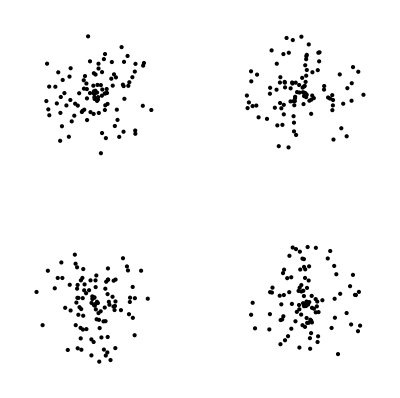

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[8,"class"],1]]]
```

```mathematica
samplesS[8]=ExportString[Flatten[samples[8,"class"],1],"TSV"]<>"\n";
```

```mathematica
(*samplesS[4]=ExportString[Join[Flatten[samples[4,"class"],1],samples[4,"background"]],"TSV"]<>"\n";*)
```

```mathematica
(*Export["./generative-data/data8.tsv",strDataToExportStr[8],"String"]*)
```

./generative-data/data8.tsv

## high Dimensional

## Experimental